# Mathematica Tutorial: Troubleshooting Code

This tutorial is entirely self-paced; you’re required to submit a minimum of five resolved errors with a brief summary of a) what was wrong and b) how you fixed it. 

Problems range in difficulty, and are not in any particular order; if you’re really stuck on something, I suggest you move on to something else.

In each problem, there should be one error to correct. Some of the errors are a result of improper Mathematica syntax, some because of incorrectly applying a command, and some are mathematical errors. Sometimes errors still result in a numerical answer. 

Remember: Mathematica is a tool, and we should still be critically assessing results to make sure they make sense! When Mathematica flags an error, yet still gives an answer, your responsibility is to determine why the error occurred, and find a way to justify the result as right or wrong.

In each case, I suggest you do not change the problematic code in the “Broken Problems” Section; instead, work in the “Solutions” section where there is an identical copy of the problems, so you can preserve the original issue and understand what changes led to the solution.

To get full marks, you must indicate why the code was wrong, and what you did to correct it (i.e. show your work). 
Email completed tutorials to me at j.ho@example.ca by MM/DD at hh:mm.

## Broken Problems

```mathematica
(*Test functions for use below*)
(* f[x], g[x], p[x], and q[x] do not contain any errors. *)
f[x_]:=Log[x]^2+BesselJ[1,x]/Sinc[x]
g[x_]:=(x^5-45 x^3+20 x^2-13x-4)/(3 x^3+4 x^2+6)
p[x_]:=x^2 Tan[Log[x]]
q[x_]:=Cos[x]/x
```

### Problem 1

General::ivar: 0.000204286 is not a valid variable.

General::ivar: 0.204286 is not a valid variable.

General::ivar: 0.408368 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

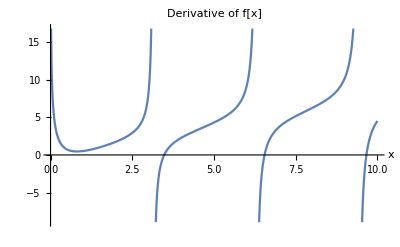

```mathematica
Plot[{f[x],D[f[x],x]},{x,0,10},PlotLabel->"Derivative of f[x]",AxesLabel->Automatic]
```

### Problem 2

```mathematica
Integrate[g[x],{x,-10,10}]
```

Integrate::idiv: Integral of (-4-13 x+20 x^2-45 x^3+x^5)/(6+4 x^2+3 x^3) does not converge on {-10,10}.

∫_-10^10 (-4-13 x+20 x^2-45 x^3+x^5)/(6+4 x^2+3 x^3)ⅆx

### Problem 3

```mathematica
Solve[{f[x]==g[x]},{x}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{Log[x]^2+BesselJ[1,x]/Sinc[x]==(-4-13 x+20 x^2-45 x^3+x^5)/(6+4 x^2+3 x^3)},{x}]

### Problem 4

```mathematica
FindRoot[{f[x]==g[x]},{x,2}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→0.497158}

### Problem 5

```mathematica
Clear[h]
h[x]=4 Exp[-x/25]
N[h[14]]
```

4 ⅇ^(-x/25)

h[14.]

### Problem 6

```mathematica
Plot[(p[y],q[y]),{y,0,10},PlotRange->{{0,4},{-2,2}}]
```

Syntax::sntxf: "(" cannot be followed by "p[y],q[y])".

### Problem 7

```mathematica
Plot[p[x],q[x],f[x],{x,-10,10},PlotRange->{{0,4},{-2,2}}]
```

Plot::nonopt: Options expected (instead of {x,-10,10}) beyond position 2 in Plot[p[x],q[x],f[x],{x,-10,10},PlotRange→{{0,4},{-2,2}}]. An option must be a rule or a list of rules.

Plot[p[x],q[x],f[x],{x,-10,10},PlotRange→{{0,4},{-2,2}}]

### Problem 8

```mathematica
Plot[j[x],{x,0,10}]
```

-Graphics-

### Problem 9

```mathematica
Plot[g[x] {x,0,10}]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[g[x] {x,0,10}]

### Problem 10

General::ivar: 0.000128356 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

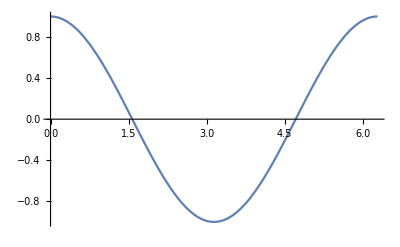

```mathematica
Plot[{Cos[x],Series[Cos[x],{x,0,4}]},{x,0,2π}]
```

### Problem 11

```mathematica
Solve[Sin[x]==x,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Sin[x]==x,x]

### Problem 12

```mathematica
g[x] //.x->x+1
```

ReplaceRepeated::rrlim: Exiting after (-4-13 x+20 x^2-45 x^3+x^5)/(6+4 x^2+3 x^3) scanned 65536 times.

(-4-13 (65536+x)+20 (65536+x)^2-45 (65536+x)^3+(65536+x)^5)/(6+4 (65536+x)^2+3 (65536+x)^3)

### Problem 13

```mathematica
FindMinimum[1/x-2Exp[-x],{x,5}]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{6.02804×10^-14,{x→1.65891×10^13}}

### Problem 14

```mathematica
FindRoot[x^2+x+1,{x,4,10}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{x→14.4992}

### Problem 15

```mathematica
soln=NSolve[{(3 x^3+4 x^2+6)g[x]==0},x][[1]]
Plot[p[y]q[soln],{y,0,10}]
```

{x→-6.93834}

-Graphics-

### Problem 16

```mathematica
Solve[{x^2+5y x - 6x+9=0, y^3-4y+6=0},{y,x}];
```

Set::write: Tag Plus in 9-6 x+x^2+5 x y is Protected.

Set::write: Tag Plus in 6-4 y+y^3 is Protected.

Solve::naqs: 0&&0 is not a quantified system of equations and inequalities.

### Problem 17

```mathematica
p[q[x]]
Findroot[%,{x,4}]
```

(Cos[x]^2 Tan[Log[Cos[x]/x]])/x^2

Findroot[(Cos[x]^2 Tan[Log[Cos[x]/x]])/x^2,{x,4}]

### Problem 18

```mathematica
Plot[e^x,{x,0,Pi}]
```

### Problem 19

```mathematica
f1[x_]:=Module[{counter},counter=0;
While[counter<5,counter+=1;
Print[counter]
If[counter>2,Return[x]];
];
];
f1[20.]
```

1

2

3

4

5

### Problem 20

```mathematica
Plot[Evaluate[u[x]/.NDSolve[{u''[x]-(x^2-k)*u[x]==0,u'[0]==0,u[0]==1},u[x],{x,0,10}]],{x,0,9},PlotRange->{-10,10}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at x == 0..

ReplaceAll::reps: {NDSolve[{-(Times[«2»]+Power[«2»]) u[x]+u''[x]==0,u'[0]==0,u[0]==1},u[x],{x,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000183857 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{-(3.38034×10^-8+Times[«2»]) u[0.000183857]+u''[0.000183857]==0,u'[0]==0,u[0]==1},u[0.000183857],{0.000183857,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000183857 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{-1. (3.38034×10^-8+Times[«2»]) u[0.000183857]+u''[0.000183857]==0.,u'[0.]==0.,u[0.]==1.},u[0.000183857],{0.000183857,0.,10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.183857 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

## Your Solutions

```mathematica
(*Test functions for use below*)
(* f[x], g[x], p[x], and q[x] do not contain any errors. *)
f[x_]:=Log[x]^2+BesselJ[1,x]/Sinc[x]
g[x_]:=(x^5-45 x^3+20 x^2-13x-4)/(3 x^3+4 x^2+6)
p[x_]:=x^2 Tan[Log[x]]
q[x_]:=Cos[x]/x
```

### Problem 1

```mathematica
Plot[{f[x],D[f[x],x]},{x,0,10},PlotLabel->"Derivative of f[x]",AxesLabel->Automatic]
```

General::ivar: 0.000204286 is not a valid variable.

General::ivar: 0.204286 is not a valid variable.

General::ivar: 0.408368 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

### Problem 2

```mathematica
Integrate[g[x],{x,-10,10}]
```

Integrate::idiv: Integral of (-4-13 x+20 x^2-45 x^3+x^5)/(6+4 x^2+3 x^3) does not converge on {-10,10}.

∫_-10^10 (-4-13 x+20 x^2-45 x^3+x^5)/(6+4 x^2+3 x^3)ⅆx

### Problem 3

```mathematica
Solve[{f[x]==g[x]},{x}]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{Log[x]^2+BesselJ[1,x]/Sinc[x]==(-4-13 x+20 x^2-45 x^3+x^5)/(6+4 x^2+3 x^3)},{x}]

### Problem 4

```mathematica
FindRoot[{f[x]==g[x]},{x,2}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→0.497158}

### Problem 5

```mathematica
Clear[h]
h[x]=4 Exp[-x/25]
N[h[14]]
```

4 ⅇ^(-x/25)

h[14.]

### Problem 6

```mathematica
Plot[(p[y],q[y]),{y,0,10},PlotRange->{{0,4},{-2,2}}]
```

Syntax::sntxf: "(" cannot be followed by "p[y],q[y])".

### Problem 7

```mathematica
Plot[p[x],q[x],f[x],{x,-10,10},PlotRange->{{0,4},{-2,2}}]
```

Plot::nonopt: Options expected (instead of {x,-10,10}) beyond position 2 in Plot[p[x],q[x],f[x],{x,-10,10},PlotRange→{{0,4},{-2,2}}]. An option must be a rule or a list of rules.

Plot[p[x],q[x],f[x],{x,-10,10},PlotRange→{{0,4},{-2,2}}]

### Problem 8

```mathematica
Plot[j[x],{x,0,10}]
```

-Graphics-

### Problem 9

```mathematica
Plot[g[x] {x,0,10}]
```

Plot::argr: Plot called with 1 argument; 2 arguments are expected.

Plot[g[x] {x,0,10}]

### Problem 10

```mathematica
Plot[{Cos[x],Series[Cos[x],{x,0,4}]},{x,0,2π}]
```

General::ivar: 0.000128356 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

### Problem 11

```mathematica
Solve[Sin[x]==x,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[Sin[x]==x,x]

### Problem 12

```mathematica
g[x] //.x->x+1
```

ReplaceRepeated::rrlim: Exiting after (-4-13 x+20 x^2-45 x^3+x^5)/(6+4 x^2+3 x^3) scanned 65536 times.

(-4-13 (65536+x)+20 (65536+x)^2-45 (65536+x)^3+(65536+x)^5)/(6+4 (65536+x)^2+3 (65536+x)^3)

### Problem 13

```mathematica
FindMinimum[1/x-2Exp[-x],{x,5}]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{6.02804×10^-14,{x→1.65891×10^13}}

### Problem 14

```mathematica
FindRoot[x^2+x+1,{x,4,10}]
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{x→14.4992}

### Problem 15

```mathematica
soln=NSolve[{(3 x^3+4 x^2+6)g[x]==0},x][[1]]
Plot[p[y]q[soln],{y,0,10}]
```

{x→-6.93834}

-Graphics-

### Problem 16

```mathematica
Solve[{x^2+5y x - 6x+9=0, y^3-4y+6=0},{y,x}];
```

Set::write: Tag Plus in 9-6 x+x^2+5 x y is Protected.

Set::write: Tag Plus in 6-4 y+y^3 is Protected.

Solve::naqs: 0&&0 is not a quantified system of equations and inequalities.

### Problem 17

```mathematica
p[q[x]]
Findroot[%,{x,4}]
```

(Cos[x]^2 Tan[Log[Cos[x]/x]])/x^2

Findroot[(Cos[x]^2 Tan[Log[Cos[x]/x]])/x^2,{x,4}]

### Problem 18

```mathematica
Plot[e^x,{x,0,Pi}]
```

### Problem 19

```mathematica
f1[x_]:=Module[{counter},counter=0;
While[counter<5,counter+=1;
Print[counter]
If[counter>2,Return[x]];
];
];
f1[20.]
```

1

2

3

4

5

### Problem 20

```mathematica
Plot[Evaluate[u[x]/.NDSolve[{u''[x]-(x^2-k)*u[x]==0,u'[0]==0,u[0]==1},u[x],{x,0,10}]],{x,0,9},PlotRange->{-10,10}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at x == 0..

ReplaceAll::reps: {NDSolve[{-(Times[«2»]+Power[«2»]) u[x]+u''[x]==0,u'[0]==0,u[0]==1},u[x],{x,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000183857 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{-(3.38034×10^-8+Times[«2»]) u[0.000183857]+u''[0.000183857]==0,u'[0]==0,u[0]==1},u[0.000183857],{0.000183857,0,10}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000183857 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{-1. (3.38034×10^-8+Times[«2»]) u[0.000183857]+u''[0.000183857]==0.,u'[0.]==0.,u[0.]==1.},u[0.000183857],{0.000183857,0.,10.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.183857 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-